# Metabolism Dynamics

```mathematica
ClearAll["Global`*"]
Clear["Global`*"]
Needs["PlotLegends`"]
<<"~thomasbuhrmann/Code/Mathematica/Dynamica/Dynamica.m";

figExpPath="~thomasbuhrmann/Documents/Publications/SMCs/figures/";
```

Dynamica (Version 1.0.5 - 12/6/11), Copyright(c) 1993-2011 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

General::obspkg: "VectorFieldPlots`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

## Import experimental data

```mathematica
dirName = "/Users/thomasbuhrmann/Experiments/Bacterium/Evo/SensorAbs/Rand/14_07_10__18_54_33"; 
dirName = "/Users/thomasbuhrmann/Experiments/Bacterium/Evo/SensorAbs/Rand/14_07_11__13_33_03"; 

SetDirectory[dirName];

dt=1/200;
data = Import["State.txt", "Table"];
stateNames=data[[1]]
state = data[[2;;-2]];
numStates=Dimensions[stateNames];
numData=Length[state]

fitXml = Import["GA_Progress.xml"];
bestFitness=Cases[fitXml,XMLElement["Generation",{_,"BestFitness"->fit_,_,_},___]->fit,Infinity];
avgFitness=Cases[fitXml,XMLElement["Generation",{_,_,"AverageFitness"->fit_,_},___]->fit,Infinity];
bestFitness=ToExpression[bestFitness];
avgFitness=ToExpression[avgFitness];
```

{Angle,AngularSpeed,Distance,Energy,Food,NeuralExtInput0,NeuralExtInput1,NeuralExtInput2,NeuralExtInput3,NeuralExtInput4,NeuralExtInput5,NeuralExtInput6,NeuralExtInput7,NeuralExtInput8,NeuralInput0,NeuralInput1,NeuralInput2,NeuralInput3,NeuralInput4,NeuralInput5,NeuralInput6,NeuralInput7,NeuralInput8,NeuralOutput0,NeuralOutput1,NeuralOutput2,NeuralOutput3,NeuralOutput4,NeuralOutput5,NeuralOutput6,NeuralOutput7,NeuralOutput8,NeuralState0,NeuralState1,NeuralState2,NeuralState3,NeuralState4,NeuralState5,NeuralState6,NeuralState7,NeuralState8,PosX,PosY,SensedEnergy,Sensor,SensorDer,Time,VelX,VelY,foodR}

12060

Import::nffil: File not found during Import.

## Functions

```mathematica
TtoI[time_]:=Floor[time/dt];
NtoI[name_]:=Position[stateNames, name][[1,1]];
NtoD[name_,t0_,tn_]:=Table[state[[i,NtoI[name]]],{i,t0,tn}];
time = Range[0,100.0,dt];
padds={{30,10},{20,20}};
plotOptions = {PlotJoined->True,ImagePadding->padds};
T=4*50+1;

SetTrial[tr_,startAt_,duration_,T_]:={i0,in}={1+TtoI[tr*T+startAt],TtoI[tr*T+startAt+duration]};
SetTrialPhase[tr_,ph_,T_:T]:={i0,in}={1+(3tr+ph)*T,(3tr+ph)*T+T -1};

TimeTrajectory[name_,t1_,t2_]:=Transpose[{time[[1;;(t2-t1+1)]],NtoD[name,t1,t2]}];
TimeTrajectoryData[data_,t1_,t2_]:=Transpose[{time[[1;;(t2-t1+1)]],data}];

TimeTrajectory2d[name1_, name2_,t0_,tn_]:=Transpose[{time[[1;;tn-t0+1]],NtoD[name1,t0,tn],NtoD[name2,t0,tn]}];

PhaseTrajectory[name1_, name2_,t0_,tn_,m1_:1,m2_:1]:=Transpose[{m1*NtoD[name1,t0,tn],m2*NtoD[name2,t0,tn]}];

PhaseTrajectory3d[name1_, name2_,name3_,t0_,tn_,m1_:1,m2_:1,m3_:1]:=Transpose[{m1*NtoD[name1,t0,tn],m2*NtoD[name2,t0,tn],m3*NtoD[name3,t0,tn]}];

TimePlot[name_,t0_,tn_,options_:{}] := ListLinePlot[TimeTrajectory[name,t0,tn], Join[plotOptions,options]];
DataPlot[data_,t0_,tn_,options_:{}] := ListLinePlot[TimeTrajectoryData[data,t0,tn], Join[plotOptions,options],AxesLabel->{"time"}];

TimePlot2d[name1_,name2_,t0_,tn_,options_:{}]:=Graphics3D[{Line[TimeTrajectory2d[name1,name2,t0,tn],VertexColors->1-Range[0,1,1/(tn-t0)]]},options,AxesLabel->{"time",name1,name2}];

PhasePlot[name1_,name2_,t0_,tn_,options_:{},m1_:1,m2_:1]:=Graphics[Line[PhaseTrajectory[name1,name2,t0,tn,m1,m2],VertexColors->0.8-Range[0,0.8,0.8/(tn-t0)]],Axes->True,AxesLabel->{name1,name2},options,AspectRatio->1.0];

PhasePlot3d[name1_,name2_,name3_,t0_,tn_,options_:{},m1_:1,m2_:1,m3_:1]:=Graphics3D[Line[PhaseTrajectory3d[name1,name2,name3,t0,tn,m1,m2,m3],VertexColors->1-Range[0,1,1/(tn-t0)]],Axes->True,AxesLabel->{name1,name2},options,AspectRatio->1.0];

Colorbar[colorFunction_: Automatic,min_:0,max_:1,divs_: 25]:=DensityPlot[y,{x,0,1},{y,min,max},AspectRatio->10,PlotRangePadding->0,PlotPoints->{2,divs},MaxRecursion->0,FrameTicks->{None,Automatic,None,None},ColorFunction->colorFunction];

G2D=Graphics[{},AlignmentPoint->Center,AspectRatio->1,Axes->False,AxesLabel->None,BaseStyle->{FontFamily->"Arial",FontSize->12},Frame->True,FrameStyle->Directive[Black],FrameTicksStyle->Directive[10,Black],ImagePadding->{{20,5},{15,5}},LabelStyle->Directive[Black],PlotRange->All,PlotRangeClipping->False,PlotRangePadding->Scaled[0.02]];

G2D2=Graphics[{},AlignmentPoint->Center,AspectRatio->1,Axes->False,AxesLabel->None,BaseStyle->{FontFamily->"Arial",FontSize->12},Frame->True,FrameStyle->Directive[Black],FrameTicksStyle->Directive[10,Black],ImagePadding->{{20,5},{15,5}},LabelStyle->Directive[Black],PlotRangeClipping->True,PlotRangePadding->Scaled[0.02]];

G3D=Graphics[{},AlignmentPoint->Center,BaseStyle->{FontFamily->"Arial",FontSize->10},ImagePadding->{{20,5},{15,10}},LabelStyle->Directive[Black]];

Rastered[g_,fnm_,size_,options_]:=Module[{g1,axes,plot},
g1=Show[g,options,ImageSize->size];
(*axes=Graphics[{},FilterRules[AbsoluteOptions[g1],Except[FrameTicks]]];*)
axes=Graphics[{},AbsoluteOptions[g1]];
plot=Show[g1,FrameStyle->Directive[Opacity[0]]];
plot=Magnify[plot,5];
plot=Rasterize[plot,"Image",Background->None];
(*plot=ImageResize[Rasterize[plot,"Image",ImageResolution->72*2,Background->None],Scaled[1/2]];*)
plot =Show[plot,ImageSize->ImageDimensions[axes]];
Export[fnm<> "Axes.eps",axes];
Export[fnm<>"Plot.png",plot];
Overlay[{plot,axes}]
];

Rastered3d[g_,fnm_,size_,options_]:=Module[{g1,axes,plot},
g1=Show[g,options,ImageSize->size];
axes=Graphics3D[{},FilterRules[AbsoluteOptions[g1],Except[FrameTicks]]];
plot=Show[g1,Boxed->False,BoxStyle->Directive[Opacity[0]],AxesStyle->Directive[Opacity[0]]];
plot=Magnify[plot,2];
plot=Rasterize[plot,"Image",Background->None,ImageResolution->72];
(*plot=ImageResize[Rasterize[plot,"Image",ImageResolution->72*2,Background->None],Scaled[1/2]];*)
plot =Show[plot,ImageSize->ImageDimensions[axes]];
Export[fnm<> "Axes.eps",axes];
Export[fnm<>"Plot.png",plot, Background->None];
Overlay[{axes,plot}]
];
```

## Fitness

```mathematica
bestFitP =ListLinePlot[bestFitness,PlotStyle->Black,PlotRange->All,ImageSize->400,AxesLabel->{"Generation", "Fitness"}];
avgFitP =ListLinePlot[avgFitness,PlotStyle->Gray,PlotRange->All,ImageSize->400];
Show[bestFitP, avgFitP]
maxFit = Max[bestFitness]
```

ListLinePlot::lpn: {{}} is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[{}, PlotStyle → GrayLevel[0], PlotRange → All, ImageSize → 400, AxesLabel → {"Generation", "Fitness"}], ListLinePlot[{}, PlotStyle → GrayLevel[0.5], PlotRange → All, ImageSize → 400]].

Show[ListLinePlot[{},PlotStyle→GrayLevel[0],PlotRange→All,ImageSize→400,AxesLabel→{Generation,Fitness}],ListLinePlot[{},PlotStyle→GrayLevel[0.5],PlotRange→All,ImageSize→400]]

-∞

## Trajectories

{604,803}

200

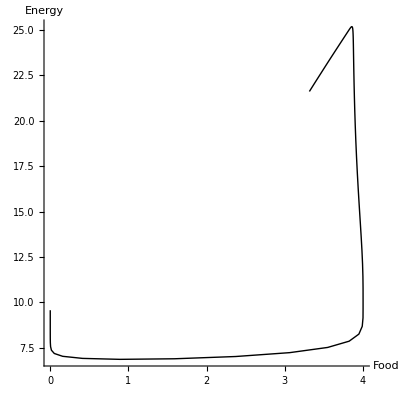

```mathematica
{t1,t2}=SetTrialPhase[0,3]
Length[NtoD["Energy",t1,t2]]
pr={{0,4},{0,10}};
pr=All;
enPhPl=PhasePlot["Food","Energy",t1,t2,{PlotRange->pr}];
Show[enPhPl]
```

## Define DS

```mathematica
meta= DynamicalSystem[
{-A-0.075A^3+0.5A^2F},
{{A,-1,30}},
{{F,0,4}}];
```

## Bifurcation Diagram

```mathematica
(*Manipulate[DisplayPhasePortrait[meta/.F->f],{f,0,10}]*)
(*EquilibriumPoints[meta/.F->1.1]*)
```

Warning: MaxSteps exceeded, terminating branch

Warning: MaxSteps exceeded, terminating branch

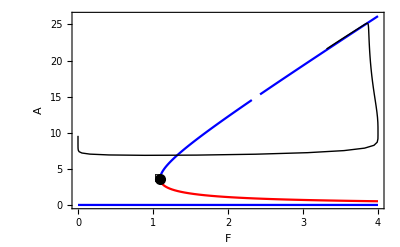

{BifurcationPoint[Fold,{3.65148371670111},{F → 1.09544511501033}]}

```mathematica
bfPl=DisplayBifurcationDiagram[meta,F];
Show[bfPl,enPhPl]
$BifurcationDiagramBPs
```

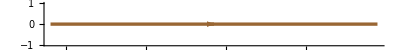

```mathematica
(*DisplayVectorField[meta/.F->2]*)
tr=DisplayTrajectories[meta/.F->2,{{2}},2] (* params: initial condition, time *)

Manipulate[Show[DisplayFlow[meta/.F->f,20.0],DisplayPhasePortrait[meta/.F->f]],{f,0,3}]
```

```mathematica
Manipulate[Show[Plot[-A-0.075A^3+0.5A^2*f,{A,-1,10}],DisplayPhasePortrait[meta/.F->f],DisplayFlow[meta/.F->f,5]],{f,0,4}]
```

## Time trajectories

```mathematica
kb=0.45;
kf=1;
kd=1;
ODE[F_,kb_,kf_,kd_]:=A'[t]==-(kb/6*A[t]^3)+(kf/2*F*A[t]^2)-kd*A[t];

T=10;
ODEsol[F_,a_]:=NDSolve[{ODE[F,kb,kf,kd],A[0]==a},A[t],{t,0,T}];
ODETrajectory[F_,a_]:=Plot[Evaluate[A[t]/.ODEsol[F,a]],{t,0,T},PlotStyle -> Black,PlotRange->All];
```

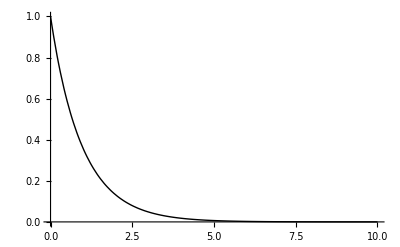

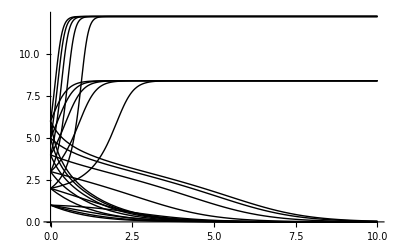

```mathematica
ODETrajectory[0,1]
Show[Table[ODETrajectory[f,a],{f,0.5,2,0.5},{a,1,6,1}],PlotRange->All]
```